-Graphics-

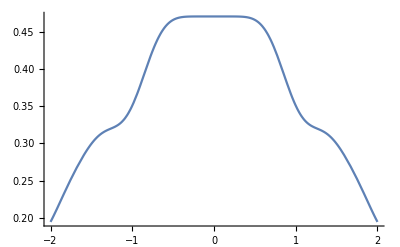

```mathematica
(*Normalized energy densiy of the SPPV field with respect to \epsilon_0 S(z,\omega). 20180815 *)
λ=632.8;
ϵr=-15.847+1.076 *I;
kx=(2Pi)/λ*√(ϵr/(ϵr+1));kz=-(2Pi)/λ*√(1/(ϵr+1));k0=2Pi/λ;
a=1/Im[kx];λspp=2Pi/Re[kx];
ρ=√(x^2+y^2)*λ;
fx[x_,y_]=(1/8)*(1/(Abs[kx]^2+Abs[kz]^2))*Sum[(Abs[kz]^2+k0^2)*(Abs[BesselJ[n+1,kx*ρ]]^2+Abs[BesselJ[n-1,kx*ρ]]^2)+2*Abs[kx]^2*Abs[BesselJ[n,kx*ρ]]^2,{n,-4,10}];
DensityPlot[fx[x,y],{x,-2,2},{y,-2,2},ColorFunction->"Rainbow",PlotRange->All,PlotPoints->200,PlotRangePadding->None,ImageSize->500,Frame->False,PlotLegends->Automatic]
Plot[fx[x,0],{x,-2,2},PlotRange->All]
```

Simulation of the SPPV field. The average OAM are 0, 4, 6, -6 for three modes fields. 

OAM = 0, modes: -1, 0, 1;
OAM = 4, modes: 3, 4, 5;
OAM = 6, modes: 5, 6, 7;
OAM = -6, modes: -7, -6, -5;

Second simulation. The OAM = 3, the mode number =  1, 5, 9, 15.
For the m.n. = 1, the modes: = 3
For the m.n. = 5, the modes: = 1, 2, 3, 4, 5.
For the m.n. = 9, the modes: = -1 t0 7.
For the m.n. = 15, the modes: = -4 to 10. 

The figures includs the energy density and the Ponting vector.